# Coupled square well scattering and bound states

## A “simple” multichannel model

## 1-channel square well

As a preliminary to the multichannel case, we will need to solve the single channel case to understand where the bound states are with respect to the threshold.  This will help us interpret the two-channel resonances, at least in the weak coupling regime.  Inside the well of range r_0, the wavefunction satisfies:

(∂^2/(∂r^2)+(2μ)/ℏ^2(E+V_0)-(L(L+1))/r^2)r ψ=0

Let k^2=(2μ r_0^2 E)/ℏ^2 and γ^2=(2μ r_0^2 V_0)/ℏ^2.  Also RESCALE r→r/r_0.  Then

(∂^2/(∂r^2)+k^2+γ^2-(L(L+1))/r^2)r ψ=0

Let β^2=k^2+γ^2, and divide through by β^2

(∂^2/(∂(β r)^2)+1-(L(L+1))/(β r)^2)r ψ=0

The fundamental unit of length is r_0, the unit of energy is ℏ^2/(2μ r_0^2).

Then inside,

rψ_in(β r)= r j_l(β r)

Outside,

rψ_out(k r)= r k_l(κ r)

with κ^2=-2μ E/ℏ^2.  or.

ψ_in=j_l(β r)

ψ_out=k_l(κ r)

matcing the log-derivatives gives:

```mathematica
Clear[V0]
```

```mathematica
SphericalBesselK[L_,z_]:=√(π/(2z))BesselK[L+1/2,z]
```

```mathematica
TEQ0=FullSimplify[D[Log[SphericalBesselJ[L,β r]],r]-D[Log[SphericalBesselK[L,κ r]],r]/.{L->0,r->1,β->√(EE+V0),k->√EE,κ->√-EE}]
```

√-EE+√(EE+V0) Cot[√(EE+V0)]

Let’s make this easier to handle by multiplying through by sin(√(E+V_0)) (it’s all equal to zero anyhow, so this doesn’t change the position of the roots.)

For s-waves:

```mathematica
TEQ0=FullSimplify[Sin[√(EE+V0)](D[Log[SphericalBesselJ[L,β r]],r]-D[Log[SphericalBesselK[L,κ r]],r])/.{L->0,r->1,β->√(EE+V0),k->√EE,κ->√-EE}]
```

√(EE+V0) Cos[√(EE+V0)]+√-EE Sin[√(EE+V0)]

for p-waves:

```mathematica
TEQ1=FullSimplify[FunctionExpand[(D[Log[SphericalBesselJ[L,β r]],r]-D[Log[SphericalBesselK[L,κ r]],r])/.{L->1,r->1,β->√(EE+V0),k->√EE,κ->√-EE}]]
```

-(√(EE+V0) (EE √(EE+V0) Cos[√(EE+V0)]+(V0+√-EE (EE+V0)) Sin[√(EE+V0)]))/((1+√-EE) ((EE+V0) Cos[√(EE+V0)]-√(EE+V0) Sin[√(EE+V0)]))

```mathematica
TEQ1=FullSimplify[FunctionExpand[(1+√-EE) ((EE+V0) Cos[√(EE+V0)]-√(EE+V0) Sin[√(EE+V0)])(D[Log[SphericalBesselJ[L,β r]],r]-D[Log[SphericalBesselK[L,κ r]],r])/.{L->1,r->1,β->√(EE+V0),k->√EE,κ->√-EE}]]
```

-√(EE+V0) (EE √(EE+V0) Cos[√(EE+V0)]+(V0+√-EE (EE+V0)) Sin[√(EE+V0)])

and for d-waves:

```mathematica
TEQ2=FullSimplify[FunctionExpand[(D[Log[SphericalBesselJ[L,β r]],r]-D[Log[SphericalBesselK[L,κ r]],r])/.{L->2,r->1,β->√(EE+V0),k->√EE,κ->√-EE}]]
```

(√(EE+V0) ((-EE)^(5/2)-3 √-EE V0+(3+√-EE) EE V0) Cos[√(EE+V0)]-(EE^3-3 √-EE V0+EE (3+EE) V0) Sin[√(EE+V0)])/((-3 √-EE+(3+√-EE) EE) (3 √(EE+V0) Cos[√(EE+V0)]+(-3+EE+V0) Sin[√(EE+V0)]))

```mathematica
TEQ2=FullSimplify[FunctionExpand[((-3 √-EE+(3+√-EE) EE) (3 √(EE+V0) Cos[√(EE+V0)]+(-3+EE+V0) Sin[√(EE+V0)]))(D[Log[SphericalBesselJ[L,β r]],r]-D[Log[SphericalBesselK[L,κ r]],r])/.{L->2,r->1,β->√(EE+V0),k->√EE,κ->√-EE}]]
```

√(EE+V0) ((-EE)^(5/2)-3 √-EE V0+(3+√-EE) EE V0) Cos[√(EE+V0)]-(EE^3-3 √-EE V0+EE (3+EE) V0) Sin[√(EE+V0)]

For purposes of rootfinding, we’ll need to make a guess as to where the roots are.  Since we know the solutions in the interior region are simply besselfunctions, we can find approximate positions of the roots by treating the finite well like an infinite well and using the known zeroes of the Bessel function.  The additional “fudge factor” of (π/4 n)^2 seems to work well in correcting the high-lying states.

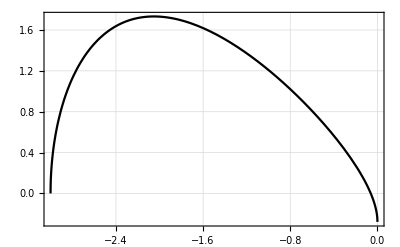

```mathematica
Vmax=3;
rootguess0=Table[{-Vmax+N[BesselJZero[1/2,n]]^2-(π/4 n)^2,0},{n,1,20}];
p2=ListPlot[rootguess0,PlotStyle->Green];
p3=Plot[√(EE+V0) Cos[√(EE+V0)]+√-EE Sin[√(EE+V0)]/.V0->Vmax,{EE,-Vmax,0},PlotStyle->Black];Show[{p2,p3},PlotRange->{{-Vmax,0},All},Frame->True,GridLines->Automatic]
```

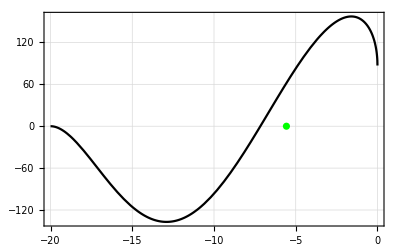

```mathematica
Vmax=20;
rootguess1=Table[{-Vmax+N[BesselJZero[3/2,n]]^2-(2.4 n)^2,0},{n,1,20}];
p2=ListPlot[rootguess1,PlotStyle->Green];
p3=Plot[TEQ1/.V0->Vmax,{EE,-Vmax,0},PlotStyle->Black];Show[{p2,p3},PlotRange->{{-Vmax,0},All},Frame->True,GridLines->Automatic]
```

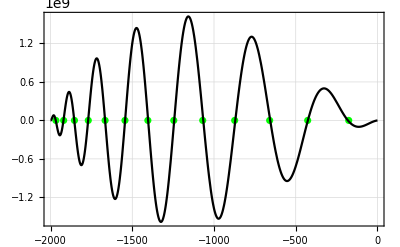

```mathematica
Vmax=2000;
rootguess2=Table[{-Vmax+N[BesselJZero[5/2,n]]^2-(π/4 n)^2,0},{n,1,20}];
p2=ListPlot[rootguess2,PlotStyle->Green];
p3=Plot[TEQ2/.V0->Vmax,{EE,-Vmax,0},PlotStyle->Black];Show[{p2,p3},PlotRange->{{-Vmax,0},All},Frame->True,GridLines->Automatic]
```

```mathematica
rootguess0=Select[Table[{-Vmax+N[BesselJZero[1/2,n]]^2-(π/4 n)^2,0},{n,1,50}],#[[1]]<100&]
```

{{-1990.75,0},{-1962.99,0},{-1916.73,0},{-1851.96,0},{-1768.68,0},{-1666.9,0},{-1546.62,0},{-1407.82,0},{-1250.53,0},{-1074.72,0},{-880.417,0},{-667.603,0},{-436.285,0},{-186.46,0},{81.8697,0}}

It’s also very helpful to know when there is a state at threshold.  So for what V_0 is the energy zero?

```mathematica
V0roots0=Sort[DeleteDuplicates[Table[V0/.FindRoot[TEQ0/.EE->0,{V0,Vn}],{Vn,2,Vmax,1}],(Abs[#1-#2]<10^-4&)]]
```

{9.13194×10^-22+0. ⅈ,2.4674,22.2066,61.685,120.903,199.859,298.556,416.991,555.165,713.079,890.732,1088.12,1305.26,1542.13,1798.74,2075.08,2371.17,2687.,3022.57,3377.87,4147.7,4562.22,4996.49,6417.71,6930.93,8016.59}

```mathematica
V0roots0Table=Table[{V0roots0[[n]],0},{n,1,Length[V0roots0]}]
```

{{9.13194×10^-22+0. ⅈ,0},{2.4674,0},{22.2066,0},{61.685,0},{120.903,0},{199.859,0},{298.556,0},{416.991,0},{555.165,0},{713.079,0},{890.732,0},{1088.12,0},{1305.26,0},{1542.13,0},{1798.74,0},{2075.08,0},{2371.17,0},{2687.,0},{3022.57,0},{3377.87,0},{4147.7,0},{4562.22,0},{4996.49,0},{6417.71,0},{6930.93,0},{8016.59,0}}

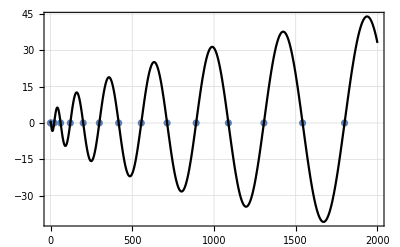

```mathematica
pv0=ListPlot[V0roots0Table];p0=Plot[TEQ0/.{EE->0},{V0,0,Vmax},PlotStyle->Black];Show[{pv0,p0},PlotRange->{{0,Vmax},All},Frame->True,GridLines->Automatic]
```

```mathematica
V0roots0[[2]]
```

2.4674

```mathematica
EE/.FindRoot[TEQ0/.V0->Vmax,{EE,-Vmax+N[BesselJZero[1/2,n]]^2-(π/4 n)^2}]/.n->1
```

-4.62419

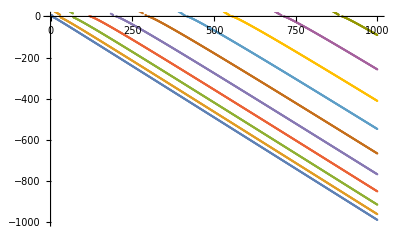

```mathematica
Vmax=1000;ListPlot[Table[{VV,EE/.FindRoot[TEQ0/.V0->VV,{EE,-VV+N[BesselJZero[1/2,n]]^2-(π/4 n)^2}]},{n,1,10},{VV,2.5,Vmax}],PlotRange->{{0,Vmax},{-Vmax,0}}]
```

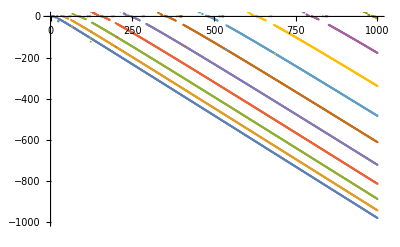

```mathematica
Vmax=1000;ListPlot[Table[{VV,EE/.FindRoot[TEQ1/.V0->VV,{EE,-VV+N[BesselJZero[3/2,n]]^2-(π/4 n)^2}]},{n,1,10},{VV,3,Vmax}],PlotRange->{{0,Vmax},{-Vmax,0}}]
```

## Generalize to N channels...

Let’s imagine a two-body Hamiltonian in relative coordinates that is of the form:

H=T+V

V=(V_11 | V_12 | V_13 | ⋯
V_21 | V_22 | V_23 | ⋯
V_31 | V_32 | V_33 | ⋯
⋮ | ⋮ | ⋮ | ⋱)

## scratch...

```mathematica
Clear[k]
```

```mathematica
ψphys=({{ⅇ^(ⅈ k r)S-ⅇ^(-ⅈ k r)}, {n ⅇ^(-q r)}})
```

{{-ⅇ^(-ⅈ k r)+ⅇ^(ⅈ k r) S},{ⅇ^(-q r) n}}

```mathematica
FullSimplify[D[ψphys,r]]
```

{{ⅈ ⅇ^(-ⅈ k r) k (1+ⅇ^(2 ⅈ k r) S)},{-ⅇ^(-q r) n q}}

```mathematica
SphericalBesselK[L_,z_]:=√(π/(2z))BesselK[L+1/2,z]
```

```mathematica
Simplify[FunctionExpand[x SphericalBesselK[0,x]],Assumptions->{x>0}]
```

(ⅇ^-x π)/2

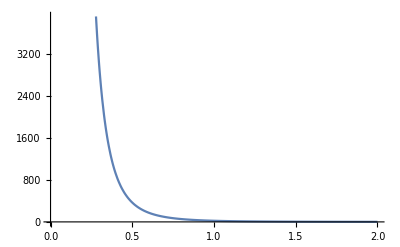

```mathematica
Plot[SphericalBesselK[3,x],{x,0,2}]
```

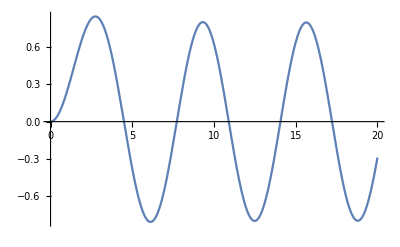

```mathematica
Plot[FullSimplify[FunctionExpand[√x BesselJ[L+1/2,x],Assumptions->{L∈Integers,L>0}]]/.L->1,{x,0,20}]
```